# Diplomado en programación básica // MCTP 2023

Luis Gerardo Ramirez Archundia

07 de febrero de 2023

En la siguiente tabla se muestran las masas de los mesones pseudoescalares. La masa es obtenida usando un modelo teórico y m_ps^{exp} es la masa que se obtiene experimentalmente.

Pase esta tabla a Mathematica

```mathematica
MassTable={{"Meson", "Mass [GeV]", "mps_exp[GeV]"},{"ud̄", 0.139, 0.139}, {"us̄",0.499,0.493},{"cū",1.855,1.864},{"cs̄",1.945,1.986},{"ub̄", 5.082,5.279},{"sb̄",5.281,5.366},{"cb̄",6.138,6.274},{"cc̄",2.925,2.983},{"bb̄",9.280,9.398}}//TableForm
```

Meson | Mass [GeV] | mps_exp[GeV]
ud̄ | 0.139 | 0.139
us̄ | 0.499 | 0.493
cū | 1.855 | 1.864
cs̄ | 1.945 | 1.986
ub̄ | 5.082 | 5.279
sb̄ | 5.281 | 5.366
cb̄ | 6.138 | 6.274
cc̄ | 2.925 | 2.983
bb̄ | 9.28 | 9.398

Calcule el error entre el valor obtenido con el modelo y el valor experimental

```mathematica
Mass={{"ud̄", 0.139, 0.139}, {"us̄",0.499,0.493},{"cū",1.855,1.864},{"cs̄",1.945,1.986},{"ub̄", 5.082,5.279},{"sb̄",5.281,5.366},{"cb̄",6.138,6.274},{"cc̄",2.925,2.983},{"bb̄",9.280,9.398}}//TableForm;
MassCopia={{"ud̄", 0.139, 0.139}, {"us̄",0.499,0.493},{"cū",1.855,1.864},{"cs̄",1.945,1.986},{"ub̄", 5.082,5.279},{"sb̄",5.281,5.366},{"cb̄",6.138,6.274},{"cc̄",2.925,2.983},{"bb̄",9.280,9.398}};
error=Table[(Mass[[1,i,3]]-Mass[[1,i,2]])/Mass[[1,i,3]]*100,{i,9}];
MeV=Table[Mass[[1,i,2]]*1000,{i,9}];
s=ResourceFunction["AppendColumn"][MassCopia,error];
s1=ResourceFunction["AppendColumn"][s,MeV]//TableForm
```

ud̄ | 0.139 | 0.139 | 0. | 139.
us̄ | 0.499 | 0.493 | -1.21704 | 499.
cū | 1.855 | 1.864 | 0.482833 | 1855.
cs̄ | 1.945 | 1.986 | 2.06445 | 1945.
ub̄ | 5.082 | 5.279 | 3.73177 | 5082.
sb̄ | 5.281 | 5.366 | 1.58405 | 5281.
cb̄ | 6.138 | 6.274 | 2.16768 | 6138.
cc̄ | 2.925 | 2.983 | 1.94435 | 2925.
bb̄ | 9.28 | 9.398 | 1.25559 | 9280.

C:\Users\Mi PC\Desktop

datos.dat

Obtenga el valor de la masa en MeV. Una vez completada la tabla exportela a un archivo llamado “TablaC.dat” (Esta tabla tambíens e envía a la plataforma)

```mathematica
SetDirectory["C:\\Users\\Mi PC\\Desktop"]
Export["datos.dat",s1]
```

C:\Users\Mi PC\Desktop

datos.dat

Calcule la diferencia de masas entre todos los mesones.

```mathematica
ud=Table[Mass[[1,1,2]]-Mass[[1,i,2]],{i,9}]
us=Table[Mass[[1,2,2]]-Mass[[1,i,2]],{i,9}]
cu=Table[Mass[[1,3,2]]-Mass[[1,i,2]],{i,9}]
cs=Table[Mass[[1,4,2]]-Mass[[1,i,2]],{i,9}]
ub=Table[Mass[[1,5,2]]-Mass[[1,i,2]],{i,9}]
sb=Table[Mass[[1,6,2]]-Mass[[1,i,2]],{i,9}]
cb=Table[Mass[[1,7,2]]-Mass[[1,i,2]],{i,9}]
cc=Table[Mass[[1,8,2]]-Mass[[1,i,2]],{i,9}]
bb=Table[Mass[[1,9,2]]-Mass[[1,i,2]],{i,9}]
```

{0.,-0.36,-1.716,-1.806,-4.943,-5.142,-5.999,-2.786,-9.141}

{0.36,0.,-1.356,-1.446,-4.583,-4.782,-5.639,-2.426,-8.781}

{1.716,1.356,0.,-0.09,-3.227,-3.426,-4.283,-1.07,-7.425}

{1.806,1.446,0.09,0.,-3.137,-3.336,-4.193,-0.98,-7.335}

{4.943,4.583,3.227,3.137,0.,-0.199,-1.056,2.157,-4.198}

{5.142,4.782,3.426,3.336,0.199,0.,-0.857,2.356,-3.999}

{5.999,5.639,4.283,4.193,1.056,0.857,0.,3.213,-3.142}

{2.786,2.426,1.07,0.98,-2.157,-2.356,-3.213,0.,-6.355}

{9.141,8.781,7.425,7.335,4.198,3.999,3.142,6.355,0.}

Realice una gráfica donde se muestre la comparación entre las masas experimentales y las teóricas. (Sugerencia: use el comando BarChart)

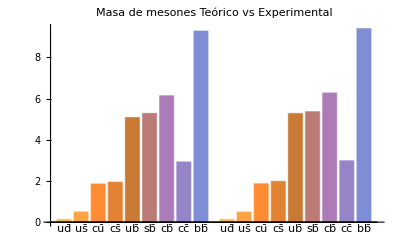

```mathematica
BarChart[{Table[Mass[[1,i,2]],{i,9}],Table[Mass[[1,i,3]],{i,9}]}, ChartLabels->{"ud̄","us̄","cū", "cs̄", "ub̄", "sb̄", "cb̄", "cc̄", "bb̄"}, PlotLabel->"Masa de mesones  Teórico vs Experimental"]
```

Implemente esta tabla en Mathematica. Primero escribela en un editor de textos e importala a Mathematica.

Usa el comando “fit” para encontrar la mejor ecuación que se ajuste a los datos.

```mathematica
data=Import["C:\\Users\\Mi PC\\Desktop\\data.csv"];
ajust=Fit[data,{Cos[x],Sin[x],Cos[x]^2,Sin[x]^2, Cos[x]^3,Sin[x]^3, Cos[x]^4, Sin[x]^4, Cos[x]^5, Sin[x]^5, Cos[x]^6, Sin[x]^6},x]
```

4.34718 Cos[x]-0.254042 Cos[x]^2-5.8631 Cos[x]^3-3.25079 Cos[x]^4+1.64814 Cos[x]^5+2.90457 Cos[x]^6+1.7314 Sin[x]+5.20923 Sin[x]^2-16.5612 Sin[x]^3+3.45543 Sin[x]^4+17.3008 Sin[x]^5-11.0007 Sin[x]^6

Gráfica la tabla junto con tu ajuste para ver que tan bueno eres.

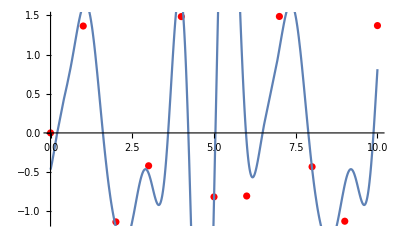

```mathematica
Show[ListPlot[data,PlotStyle->Red], Plot[ajust,{x,0,10}]]
```

Haz una tabla con los primeros 25 números pares, graficalos y has un ajuste de la curva. Exporta la tabla a “Pares.dat” (se sube a la plataforma)

2. x

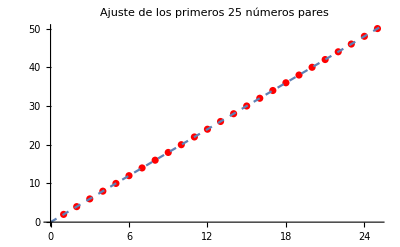

EvenNumbers.dat

```mathematica
EvenNumbers=Table[2 n,{n,25}];
FitEvenNumbers=Fit[EvenNumbers,{x},x]
Show[ListPlot[EvenNumbers, PlotStyle->Red], Plot[FitEvenNumbers,{x,0,60},PlotStyle->Dashed], PlotLabel->"Ajuste de los primeros 25 números pares"]
Export["EvenNumbers.dat",EvenNumbers]
```